## Condiciones de regularidad 3er orden β=α^2

```mathematica
fzgen=Assuming[r>0&&μ>0&&r^4>0&&α>0&&β>0,-(-7 r^2 α-36 β)/(36 β)-(-49 r^4 α^2+756 r^4 β)/(18 2^(2/3) β (686 r^6 α^3-15876 r^6 α β-27216 r^2 α β^2-27216 r^2 β^2 μ+√(4 (-49 r^4 α^2+756 r^4 β)^3+(686 r^6 α^3-15876 r^6 α β-27216 r^2 α β^2-27216 r^2 β^2 μ)^2))^(1/3))+1/(36 2^(1/3) β)(686 r^6 α^3-15876 r^6 α β-27216 r^2 α β^2-27216 r^2 β^2 μ+√(4 (-49 r^4 α^2+756 r^4 β)^3+(686 r^6 α^3-15876 r^6 α β-27216 r^2 α β^2-27216 r^2 β^2 μ)^2))^(1/3)]/.β->α^2
```

-(-7 r^2 α-36 α^2)/(36 α^2)-(707 r^4)/(18 2^(2/3) (-15190 r^6 α^3-27216 r^2 α^5-27216 r^2 α^4 μ+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 r^2 α^5-27216 r^2 α^4 μ)^2))^(1/3))+((-15190 r^6 α^3-27216 r^2 α^5-27216 r^2 α^4 μ+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 r^2 α^5-27216 r^2 α^4 μ)^2))^(1/3))/(36 2^(1/3) α^2)

```mathematica
Clear[α,μ]
μ:=1
Manipulate[Plot[-(-7 r^2 α-36 β^2)/(36 β^2)-(-49 r^4 α^2+756 r^4 β^2)/(18 2^(2/3) β^2 (686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ)^2))^(1/3))+1/(36 2^(1/3) β^2)(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ)^2))^(1/3),{r,0,6},AxesLabel->{"r","f(r)"},PlotRange->All],{α,-0.1,0.1,0.002},{β,-0.05,0.05,0.001}]
```

```mathematica
Clear[μ]
```

### ¿Para qué valores de α y β f(r) es Real?

```mathematica
rad=Simplify[Sqrt[4 (-49 r^4 α^2+756 r^4 β)^3+(686 r^6 α^3-15876 r^6 α β-27216 r^2 α β^2-27216 r^2 β^2 μ)^2]]/.r->1
```

14 √(7 (-7 α^2+108 β)^3+(7 (7 α^3-162 α β)-1944 β^2 (α+μ))^2)

```mathematica
RegionPlot3D[Im[rad]==0&&rad!=0,{α,-0.1,0.1},{β,-0.5,0.5},{μ,0,10},PlotPoints->40,MaxRecursion->2,AxesLabel->{"α","β","μ"},PlotLabel->"Región donde rad > 0"]
```

-Graphics3D-

### ¿Cómo se comporta f(r) cuando r tiende a Infinito?

```mathematica
Assuming[r>0&& α>0 &&β>0,Simplify[Series[Simplify[fzgen],{r,Infinity,2}]]]
```

((7 α+(7^(2/3) (7 α^2-108 β))/((49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))+7^(1/3) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3)) r^2)/(36 β)+1+((-1134 α^2 β+23328 β^2+7 √21 α^3 √(-7 α^2+144 β)-162 √21 α β √(-7 α^2+144 β)) (-7 7^(2/3) α^2+108 7^(2/3) β+7^(1/3) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)) (α+μ))/(9 (7 α^2-144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) r^2)+O[1/r]^3

```mathematica
Coef1=7 α+(7^(2/3) (7 α^2-108 β))/((49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))+7^(1/3) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3)
```

7 α+(7^(2/3) (7 α^2-108 β))/((49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))+7^(1/3) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3)

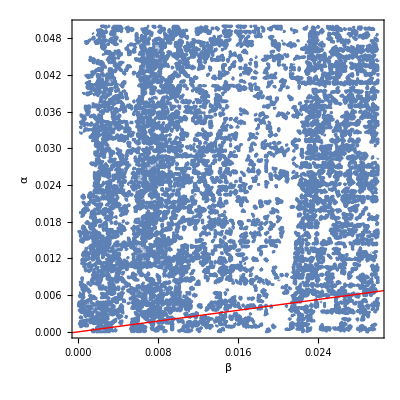

```mathematica
Assuming[α>0 &&β>0,RegionPlot[Coef1==0,{β,0,0.03},{α,0,0.05},PlotPoints->60,FrameLabel->{"β","α"},Epilog->{Thick,Red,InfiniteLine[{{0,0},{1,Sqrt[7/144]}}]}]]
```

```mathematica
Solve[Coef1==0,α]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{}}